{c→15.9203,k→0.489611,b→18.8626}

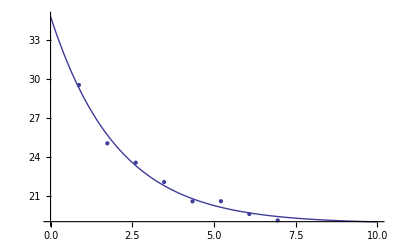

```mathematica
data = {
{0.8685714286,29.5121965714},
{1.7371428572,25.0243931429},
{2.6057142858,23.5365897143},
{3.4742857144,22.0487862858},
{4.342857143,20.5609828572},
{5.2114285716,20.5731794287},
{6.0800000002,19.5853760001},
{6.9485714288,19.0975725716}
};
model = c*Exp[-k*x]+b;
fit = FindFit[data,model,{c,k,b},x,MaxIterations->100000]
ffit = model/. fit;
plot = Plot[ffit, {x,0,10}];
pdata = ListPlot[data];
Show[plot,pdata]
```